```mathematica
(* Fuchs Nordheim Model for large reactivity insertions *)
(* Using a point reactor kinetics approximation, a simplified assumption for the
Doppler feedback and neglecting delayed neutrons, the adiabatic fuel temperature
change is modeled *)

(* fraction of delayed neutrons *)
beta=0.0075;
(* mean generation time in seconds *)
lambda = 0.001;
(* energy deposited per fission event, e.g. 200MeV in Joule *)
Ef=3.20435*10^-11;
(* macroscopic fission cross secetion in 1/cm *)
sigmaF=0.05;
(* volume of fuel in cm3, i.e. one 16x16-20 fuel assembly *)
V=72*10^3;
(* heat capacity of fuel in J/gK *)
cF=0.32;
(* Doppler temperature feedback 1/K*)
alpha=3*10^-5;
(* density of UO2 fuel g/cm3*)
rhoF=9.7;
(* reactivity insertion at t=0 *)
rhoNull=0.0025;
(* initial fuel temperature K*)
tempNull=1800;
(* initial neutron flux 1/s cm2*)
phiNull=10^14;
tempI=Ef*sigmaF*V/(cF*V*rhoF);
rho[t_,tf_]:=beta+2*rhoNull*UnitStep[t]-alpha*(tf-tempNull);

(* Fuchs-Nordheim set of equations *)
eqs={D[fuelT[t],t]==tempI*phi[t],D[phi[t],t]==phi[t]*(rho[t,fuelT[t]]-beta)/lambda};

sol=First[NDSolve[{eqs,fuelT[0]==tempNull,phi[0]==phiNull},{fuelT,phi},{t,0,10},AccuracyGoal->8]];

g1[t_]:=Evaluate[fuelT[t]/.sol[[1]]];
g2[t_]:=Evaluate[phi[t]/.sol[[2]]];

(* Let us compare that to the analytic solution: *)
(* Thankfully provided by Martin :)) *)
kappa=Sqrt[(rhoNull-beta)^2/lambda^2+2*alpha*tempI*phiNull/lambda]; 
ynull=(rhoNull-beta)/lambda;
tnull=-2*ArcTanh[(ynull/kappa)]/kappa;
phiAnalytic[t_]:=lambda*kappa^2/(2*alpha*tempI)*(1/(Cosh[kappa*(t-tnull)/2])^2)
(* Plot numeric and analytic solution for neutron flux: *)
LogPlot[{g2[t],phiAnalytic[t]},{t,0,5},PlotRange->{10^11,14*10^14}]
```

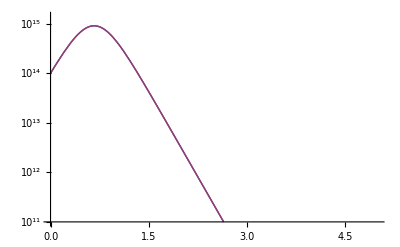

```mathematica
(* Plot solution for adiabatic temperature increase: *)
```

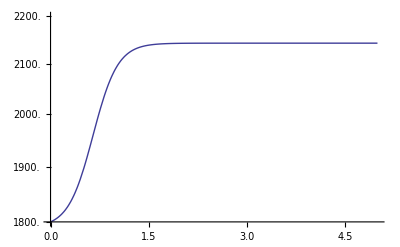

```mathematica
LogPlot[{g1[t]},{t,0,5},PlotRange->{1800,2200}]
```